# Ascii1D

The Ascii1D package provides functions for manipulating time-dependent 1D data files.

```mathematica
SetDirectory[NotebookDirectory[]<>"/.."]
```

/Users/ian/Projects/Code/nrmma

```mathematica
<<"Ascii1D.m"
```

## Reading

You can import a 1D CarpetIOASCII file:

ReadCarpetASCII1D[filename, rl, 1]

where filename is the name of the input file, rl is the refinement level to take, and dir is the direction of the data, with {1,2,3} for {x,y,z}.  The resulting structure (simulated here for the purpose of documentation) is of the form

```mathematica
data=Table[{t,MakeDataTable[Table[{x,Sin[2Pi (x-t)]},{x,0,1,0.1}]]},{t,0,1,0.1}]
```

{{0.,DataTable[...]},{0.1,DataTable[...]},{0.2,DataTable[...]},{0.3,DataTable[...]},{0.4,DataTable[...]},{0.5,DataTable[...]},{0.6,DataTable[...]},{0.7,DataTable[...]},{0.8,DataTable[...]},{0.9,DataTable[...]},{1.,DataTable[...]}}

## Using

You can plot the elements of this structure directly:

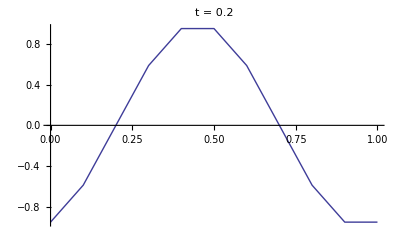

```mathematica
ListLinePlot[data[[3,2]],PlotLabel->"t = " <> ToString[data[[3,1]]]]
```

or you can use the provided functions AsciiTimeOfIndex and AsciiDataOfIndex:

```mathematica
AsciiTimeOfIndex[data,3]
```

0.2

```mathematica
AsciiDataOfIndex[data,3]
```

DataTable[...]

You can also use Manipulate to easily step through it:

```mathematica
Manipulate[ListLinePlot[data[[i,2]],PlotLabel->"t = " <> ToString[data[[i,1]]]],{i,1,Length[data],1}]
```

## Full API

The full list of Ascii1D functions is below.  Click on one of them for documentation:

```mathematica
?Ascii1D`*
```